## 1D CellPlot:

Initial Conditions:

```mathematica
basis={{1,0},{0.5,Sqrt[3]/2}}; (* A basis generating the lattice points. Length equal to dimension of lattice.*)
initialConditions1D={0,0,0,0,0,0,0,1,0,0,0,1,0,0,0}; (* Initial conditions. *)
rowLength[n_Integer]:=If[EvenQ[n],{n/2,n/2},{(n+1)/2,(n-1)/2}]; (*Specifies how many "odd" and "even" triangles are in our graphic. First value is odd trangles. *)
```

Triangular Cells 1D Case:

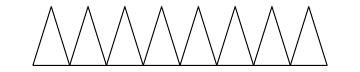

```mathematica
oddTriangles[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],r=rowLength[Length[initialConditions]][[1]]-1},
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*i+1]]]],EdgeForm[Black],Triangle[{i*b1,(i+1)*b1,i*b1+b2}]},
{i,0,r}]
]; (* Generates the "odd" traingles that can then be interpreted as Graphics objects. *)
Graphics[oddTriangles[basis,initialConditions1D]]
```

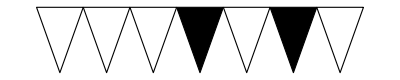

```mathematica
evenTriangles[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],r=rowLength[Length[initialConditions]][[2]]-1},
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*(i+1)]]]],EdgeForm[Black],
Triangle[{(i+1)*b1+b2,(i+1)*b1,i*b1+b2}]},
{i,0,r}]
];(* Generates the "even" traingles that can then be interpreted as Graphics objects. *)
Graphics[evenTriangles[basis,initialConditions1D]]
```

```mathematica
triangleCAList[basis_,initialConditions_]:=
Riffle[
oddTriangles[basis,initialConditions],evenTriangles[basis,initialConditions]
];  (* Combines the lists of "odd" and "even" triangles into a new list. *)
```

New generation rule:

```mathematica
ruleTable[rule_Integer,neighborCount_Integer:5]:=Reverse[PadLeft[IntegerDigits[rule,2],2^neighborCount]]; (* Given a number and Moore neighborhood size generates a rule table. *)
ruleTable[30,3]
```

{0,1,1,1,1,0,0,0}

```mathematica
nextStep[initialConditions_List,rule_Integer,neighborCount_Integer:5]:=Module[{a=neighborCount/2,b=Floor[neighborCount/2],l=Length[initialConditions]},
Table[
ruleTable[rule,neighborCount][[FromDigits[
If[i<a,PadLeft[Take[initialConditions,{1,i+b}],neighborCount],
If[i>l-a,PadRight[Take[initialConditions,{i-b,l}],neighborCount],Take[initialConditions,{i-b,i+b}]]],2]+1]]
,{i,1,l}]
]; (*Generates the state at time t+1 given state at time t. *)
```

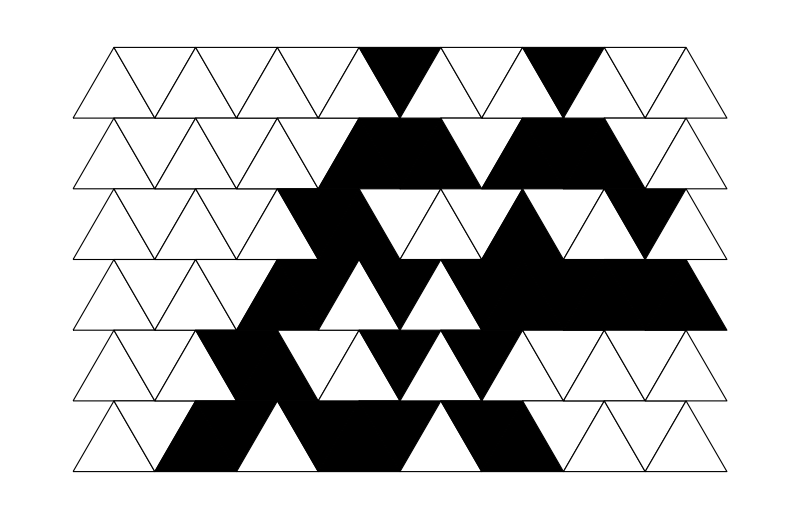

```mathematica
triangularCA[basis_,initialConditions_List,iterations_Integer,rule_Integer,neighborCount_Integer:5]:=Module[{d=basis[[1]][[2]]/2-basis[[2]][[2]],r=rowLength[Length[initialConditions]]},
Graphics[
Table[
Translate[triangleCAList[basis,Nest[nextStep[#,rule,neighborCount]&,initialConditions,i]],{0,d*i}],{i,0,iterations}
],
ImageSize->100*r[[1]]]
]; (* Plots a triangular CA *)
triangularCA[{{1,0},{0.5,Sqrt[3]/2}},initialConditions1D,5,30,3]
```

## 2D CellPlot:

2D Initial Conditions:

```mathematica
initialConditions2D=SparseArray[{{1,1}->1,{2,5}->1,{3,10}->1},{3,11}];
```

```mathematica
latticePoints[basis_,dimensions_]:=Flatten[
Table[(i*basis[[1]]+j*basis[[2]]),{i,0,dimensions[[1]]-1},{j,0,dimensions[[2]]-1}]
,1];
latticePointsPlot[points_]:=ListPlot[points,Axes->False]; (* Generates a list of 2D lattice points given a basis. *)
```

```mathematica
oddTriangleCells[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],c=Reverse[initialConditions,1],d1=Dimensions[initialConditions][[1]],
d2=If[EvenQ[Dimensions[initialConditions][[2]]],(Dimensions[initialConditions][[2]])/2,(Dimensions[initialConditions][[2]]+1)/2]},
Flatten[
Table[
{FaceForm[GrayLevel[1-c[[j+1]][[2i+1]]]],EdgeForm[Black],Triangle[{i*b1+j*b2,(i+1)*b1+j*b2,i*b1+(j+1)*b2}]}
,{i,0,d2-1},{j,0,d1-1}]
,1]
]; (* Generates a list of "odd" triangular cells of a 2D CA, given a lattice basis and initial conditions. *)
```

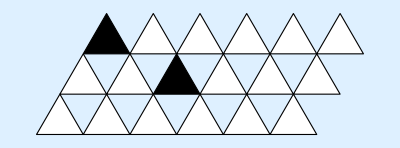

```mathematica
oddTriangleCells[basis,initialConditions2D];
Graphics[oddTriangleCells[basis,initialConditions2D],Background->LightBlue]
```

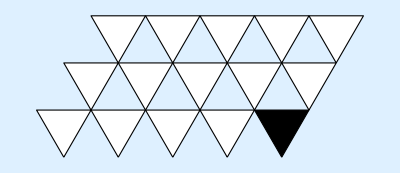

```mathematica
evenTriangleCells[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],c=Reverse[initialConditions,1],d1=Dimensions[initialConditions][[1]],
d2=If[EvenQ[Dimensions[initialConditions][[2]]],(Dimensions[initialConditions][[2]])/2,(Dimensions[initialConditions][[2]]-1)/2]},
Flatten[
Table[
{FaceForm[GrayLevel[1-c[[j+1]][[2(i+1)]]]],EdgeForm[Black],Triangle[{(i+1)*b1+j*b2,i*b1+(j+1)*b2,(i+1)*b1+(j+1)*b2}]}
,{i,0,d2-1},{j,0,d1-1}]
,1]
]; (* Generates a list of "even" triangular cells of a 2D CA, given a lattice basis and initial conditions. *)
Graphics[evenTriangleCells[basis,initialConditions2D],Background->LightBlue]
```

```mathematica
triangleCells[basis_,initialConditions_]:=Riffle[
oddTriangleCells[basis,initialConditions],evenTriangleCells[basis,initialConditions]
]; (* Combines the lists of "odd' and "even" trianular cells to make a 2D triangular CA. *)
```

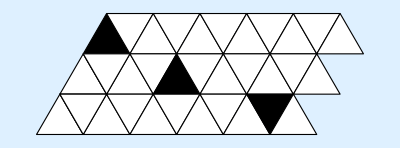

```mathematica
Graphics[triangleCells[{{1,0},{0.5,Sqrt[3]/2}},initialConditions2D],Background->LightBlue]
```

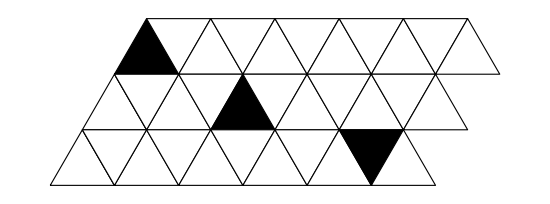

```mathematica
triangleCellPlot[basis_,initialConditions_]:=Graphics[triangleCells[basis,initialConditions],ImageSize->50*Dimensions[initialConditions][[2]]];
triangleCellPlot[basis,initialConditions2D]
```